# Channels of constant width on the sphere

## Stereographic Projection Geometry

```mathematica
n={0,0,2R};             (* North pole of sphere with centre at (0,0,R) *)
xy={x,y,0};          (* x,y coordinates in space *)
l=xy+λ(n-xy);    (* line joining (x,y) with north pole *)
d=l-{0,0,R};      (* Distance of line points to centre of sphere *)
sol=Simplify[Solve[Dot[d,d]==R^2,λ]];
p=Simplify[l/.sol][[2]];  (* Intersection of line with sphere *)
z=Simplify[({x1,x2,x3}+λ({x1,x2,x3}-n))/.Solve[x3+λ(x3-2R)==0,λ]][[1]][[1;;2]];
Print["Parametrization p = ",p];
Print["Stereographic projection z = ",z];

(* Verifying p is inverse of z *)
Print["z(p(x,y)) = ",Simplify[z/.{x1->p[[1]],x2->p[[2]],x3->p[[3]]}]]
Print["p(z(x1,x2,x3)) = ",Simplify[p/.{x->z[[1]],y->z[[2]]},x1^2+x2^2+(x3-R)^2== R^2]]

(* Metric tensor and volume form in x,y coordinates *)
px=Simplify[D[p,x]];
py=Simplify[D[p,y]];
xxC=Simplify[Dot[px,px]];
xyC=Simplify[Dot[px,py]];
yyC=Simplify[Dot[py,py]];
gxy={{xxC,xyC},{xyC,yyC}};
Print["Metric tensor in x,y coordinates = ",MatrixForm[gxy]]
μxy=Simplify[Sqrt[Det[gxy]],R>0 && x∈Reals && y∈Reals];
Print["Volume form in x,y coordinates = ", μxy];

(* Metric tensor and volume form in u,v coordinates *)
sbs={x->Exp[v]Cos[u],y->Exp[v]Sin[u]};
q={x,y}/.sbs;
qu=D[q,u];
qv=D[q,v];
uuC = Simplify[Dot[qu,(gxy/.sbs).qu]];
uvC=Simplify[Dot[qu,(gxy/.sbs).qv]];
vvC = Simplify[Dot[qv,(gxy/.sbs).qv]];
guv = {{uuC,uvC},{uvC,vvC}};
μuv=Simplify[Sqrt[Det[guv]],R>0&& v∈Reals];
Print["Metric tensor in u,v coordinates = ", MatrixForm[guv]]
Print["Volume form in u,v coordinates = ", μuv]
Print["gxy when R tends to infinity : ",MatrixForm[Limit[gxy,R->Infinity]]];
Print["guv when R tedns to infinity : ",MatrixForm[Limit[guv,R->Infinity]]];

(* Plotting stereographic projection *)

sz=4;R0=1;x0=1;y0=-1;mesh0=12;
planeG=ParametricPlot3D[{x,y,0},{x,-sz,sz},{y,-sz,sz},Mesh->mesh0,PlotStyle->Directive[Opacity[.99]],PlotPoints->100];
sphereMeshG=ParametricPlot3D[p/.R->R0,{x,-sz,sz},{y,-sz,sz},PlotPoints->150,Mesh->mesh0,PlotStyle->Directive[Opacity[1]]];
sphereG=ContourPlot3D[x0^2+x1^2+(x3-R0)^2==.98R0^2,{x0,-R0,R0},{x1,-R0,R0},{x3,0,2R0},Mesh->None,
ContourStyle->Directive[Opacity[.3],Specularity[1]] ];
lineG=Graphics3D[{Thick,Line[{{0,0,2R0},{x0,y0,0}}]}];
Show[lineG,sphereMeshG,sphereG,planeG,Boxed->False,Axes->False,PlotRange->{{-sz,sz},{-sz,sz},{0,sz}}]
```

Parametrization p = {(4 R^2 x)/(4 R^2+x^2+y^2),(4 R^2 y)/(4 R^2+x^2+y^2),(2 R (x^2+y^2))/(4 R^2+x^2+y^2)}

Stereographic projection z = {-(2 R x1)/(-2 R+x3),-(2 R x2)/(-2 R+x3)}

z(p(x,y)) = {x,y}

p(z(x1,x2,x3)) = {x1,x2,x3}

Metric tensor in x,y coordinates = ((16 R^4)/((4 R^2+x^2+y^2)^2) | 0
0 | (16 R^4)/((4 R^2+x^2+y^2)^2))

Volume form in x,y coordinates = (16 R^4)/((4 R^2+x^2+y^2)^2)

Metric tensor in u,v coordinates = ((16 ⅇ^(2 v) R^4)/((ⅇ^(2 v)+4 R^2)^2) | 0
0 | (16 ⅇ^(2 v) R^4)/((ⅇ^(2 v)+4 R^2)^2))

Volume form in u,v coordinates = (16 ⅇ^(2 v) R^4)/((ⅇ^(2 v)+4 R^2)^2)

gxy when R tends to infinity : (1 | 0
0 | 1)

guv when R tedns to infinity : (ⅇ^(2 v) | 0
0 | ⅇ^(2 v))

-Graphics3D-

## Annulus on the sphere

ρ(h)=-(2 R √(R^2-(-h+R)^2))/(h-2 R)

h(ρ) = (2 R ρ^2)/(4 R^2+ρ^2)

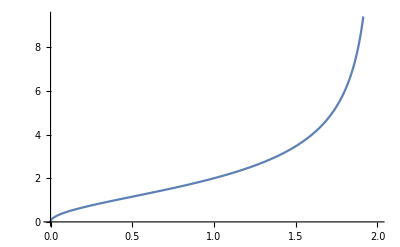

-Graphics3D-

```mathematica
ρ[h_]:=(z/.{x1->Sqrt[ R^2-(R-h)^2],x2->0,x3->h})[[1]]
Print["ρ(h)=",ρ[h]]
hρ=Simplify[h/.Solve[ρ[h]==ρ,h]][[1]];
h[ρ_]:=Evaluate[hρ]
Print["h(ρ) = ", h[ρ]]
Plot[ρ[h]/.R->R0,{h,0,2}]
(*Simplify[ρ[h[x]],R>0 && x>0]
Simplify[h[ρ[x]],R>0 && x>0]*)
h1= (1/8)R0;
h2=(3/8)1.5R0;
annulus3DG=ContourPlot3D[x0^2+x1^2+(x3-R0)^2==.99R0^2,{x0,-sz,sz},{x1,-sz,sz},{x3,0,2sz},Mesh->None,
ContourStyle->Directive[Green,Opacity[1]], RegionFunction->Function[{x,y,z},h1<z<h2],
PlotPoints->100];
annulus2DG=ParametricPlot3D[{r Cos[θ],r Sin[θ],.01},{r,ρ[h1]/.R->R0,ρ[h2]/.R->R0},{θ,0,2Pi},
PlotPoints->100,PlotStyle->Directive[Green,Opacity[.99]],Mesh->None
,BoundaryStyle->Directive[Thick,Black]];
s1G=ParametricPlot3D[{r Cos[θ],r Sin[θ],2R0-2R0 r /(ρ[h1]/.R->R0)},{r,0,ρ[h1]/.R->R0},{θ,0,2Pi},
Mesh->None,PlotStyle->Directive[Opacity[.2]],PlotPoints->100];
s2G=ParametricPlot3D[{r Cos[θ],r Sin[θ],2R0-2R0 r /(ρ[h2]/.R->R0)},{r,0,ρ[h2]/.R->R0},{θ,0,2Pi},
Mesh->None,PlotStyle->Directive[Opacity[.2]],PlotPoints->100];
planeG=ParametricPlot3D[{x,y,0},{x,-sz,sz},{y,-sz,sz},Mesh->None,PlotStyle->Directive[Gray,Opacity[.2]],PlotPoints->100];
Show[annulus3DG,annulus2DG,sphereG,planeG,s1G,s2G,Boxed->False,Axes->False]
```

```mathematica
(* Computing σ and J *)
Clear[h1,h2]
σPrim=Simplify[Integrate[μuv,v],R>0&& v∈Reals]
σ=Simplify[(σPrim/.v->Log[ρ[h2]])-(σPrim/.v->Log[ρ[h1]])]
j=Simplify[(1/2)Log[ρ[h2]^2/ρ[h1]^2],R>0&&h1∈Reals && h2∈Reals]
Limit[σ/.{h1->h[r1],h2->h[r2]},R->Infinity]
Limit[j/.{h1->h[r1],h2->h[r2]},R->Infinity]
```

-(8 R^4)/(ⅇ^(2 v)+4 R^2)

(-h1+h2) R

1/2 Log[(h2 (h1-2 R))/(h1 (h2-2 R))]

1/16 (-8 r1^2+8 r2^2)

1/2 Log[r2^2/r1^2]

## Geodesic curvature on sphere

(h-R)/(R √(R^2-(-h+R)^2))

True

-(2 R)/(R κ-√(1+R^2 κ^2))

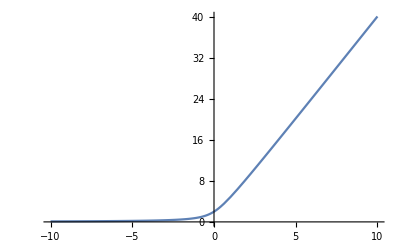

-Graphics-

```mathematica
κg[α_]:=Module[{αt,αtt,sn},
αt=Simplify[D[α,t]];
αtt=Simplify[D[αt,t]];
sn=(α-{0,0,R})/R; (* Sphere normal *)
Simplify[Dot[αtt,Cross[sn,αt]]/Dot[αt,αt]^(3/2),R>0]
];

γ=Sqrt[R^2-(h-R)^2]{Cos[t],Sin[t],0}+{0,0,h};
κgγ=(h-R)/(R Sqrt[R^2-(R-h)^2])

Simplify[κg[γ]==κgγ,R>0 && κ>0]
ρκ=Simplify[ρ[h]/.h->(R+R Sin[ArcTan[R κ]]),R>0&& κ∈Reals]
ρk2=2R(Sqrt[1+R^2κ]+R κ);
Plot[ρκ/.R->1,{κ,-10,10}]
Plot[ρκ/.R->1,{κ,-10,10}]
```

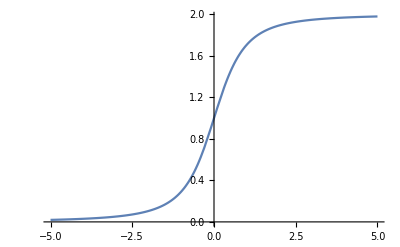

{(R (1+k^2 R^2-k R √(1+k^2 R^2)))/(1+k^2 R^2),(R (1+k^2 R^2+k R √(1+k^2 R^2)))/(1+k^2 R^2)}

```mathematica
hκ=Simplify[R+R Sin[ArcTan[R κ]]];
Plot[hκ/.R->1,{κ,-5,5}]
Simplify[h/.Solve[κgγ==k,h],k>0 && R>0]
```

## Channel of constant width

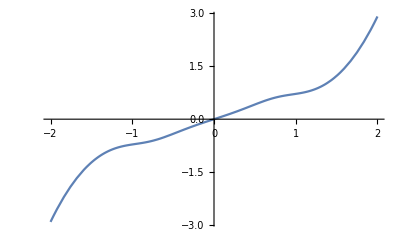

a: 1.

b: 1.

c: 0.+0. ⅈ

-Graphics3D-

-Graphics3D-

```mathematica
(* Parameters *)
R0 = 1;
uMin = -2;
uMax = 2;
wd =Pi/8;

(* Curve over sphere *)
np={0,0,R0};
α={Cos[2u],Sin[2u],.5u^3}+np;
α=np+R0 Simplify[(α-np)/Sqrt[Dot[(α-np),(α-np)]]];

(*hh=1.5;
rr = Sqrt[R0^2-(R0-hh)^2];
α={rr Cos[u],rr Sin[u],hh};*)

κgα=FullSimplify[κg[α/.u->t]/.R->R0,t∈Reals]/.t->u ;(* Geodesic curvature *)

Plot[κgα,{u,uMin,uMax}]

αtgt=Simplify[D[α,u]]; (* Unit tangent to sphere *)
αnrm=Simplify[Cross[Cross[αtgt,D[αtgt,u]],αtgt]];
αtgt=Simplify[αtgt/Sqrt[Dot[αtgt,αtgt]]];
αnrm=Simplify[αnrm/Sqrt[Dot[αnrm,αnrm]]];
β=np+(Cos[v](α-np)+Sin[v]Cross[α-np,αtgt]);
u0=.5uMin+.5uMax;
p0=α/.u->u0;
zHat=Cross[αtgt,αnrm]/.u->u0;
κgα0=κgα/.u->u0;
h0=hκ/.{R->R0,κ->κgα0};
θh=ArcSin[(h0-R0)/R0];
hp=R0+R0 Sin[θh+wd/(2R0)];
hm=R0+R0 Sin[θh-wd/(2R0)];

r0=Sqrt[R0^2-(h0-R0)^2];
rp=Sqrt[R0^2-(hp-R0)^2];
rm=Sqrt[R0^2-(hm-R0)^2];
γ0= (np -R0 zHat)+h0 zHat + r0(Cos[t](αtgt/.u->u0)+Sin[t](αnrm/.u->u0));
γp=(np -R0 zHat)+hp zHat + rp(Cos[t](αtgt/.u->u0)+Sin[t](αnrm/.u->u0));
γm=(np -R0 zHat)+hm zHat + rm(Cos[t](αtgt/.u->u0)+Sin[t](αnrm/.u->u0));
γ=(np -R0 zHat)+hv zHat + 1.01Sqrt[R0^2-(hv-R0)^2](Cos[t](αtgt/.u->u0)+Sin[t](αnrm/.u->u0));(Cos[t](αtgt/.u->u0)+Sin[t](αnrm/.u->u0));
c0=R0 zHat;
γG=ParametricPlot3D[γ,{t,0,2Pi},{hv,hm,hp},PlotStyle->Directive[Blue,Opacity[.5]],Mesh->None];
c0G = Graphics3D[{Green,PointSize[Large],Point[c0]}];
p0G=Graphics3D[{Green,PointSize[Large],Point[p0]}];
γ0G=ParametricPlot3D[γ0,{t,0,2Pi},PlotStyle->{Red}];
γpG=ParametricPlot3D[γp,{t,0,2Pi},PlotStyle->{Red}];
γmG=ParametricPlot3D[γm,{t,0,2Pi},PlotStyle->{Red}];
αG=ParametricPlot3D[α,{u,uMin,uMax}];
βG=ParametricPlot3D[β,{u,uMin,uMax},{v,-wd/2,wd/2},Mesh->None,PlotPoints->100];
sG=ContourPlot3D[x^2+y^2+(z-R0)^2==.99R0^2,{x,-R0,R0},{y,-R0,R0},{z,0,2R0},Mesh->None,ContourStyle->Directive[Gray,Opacity[.3],Specularity[1]]];
γt=γ/.t->u0;
crossG=ParametricPlot3D[β/.u->u0,{v,-wd/2,wd/2},PlotStyle->Directive[Blue]];

Print["a: ",Norm[αtgt/.u->u0]]
Print["b: ",Norm[αnrm/.u->u0]]
Print["c: ",Dot[αtgt/.u->u0,αnrm/.u->u0]]
 Show[crossG,αG,βG,γmG,γpG,γG,sG,Boxed->False, Axes->False] 
Show[crossG,αG,βG,sG,Boxed->False,Axes->False]
```